```mathematica
(*Mathematica*)
```

```mathematica
(*https://oeis.org/A175739*)
```

```mathematica
p[x_,n_]=If[n==0,1,x^(2*n)-x^(2*n-1)-x^n-x+1];
```

```mathematica
Table[p[x,i],{i,20}]
```

{1-3 x+x^2,1-x-x^2-x^3+x^4,1-x-x^3-x^5+x^6,1-x-x^4-x^7+x^8,1-x-x^5-x^9+x^10,1-x-x^6-x^11+x^12,1-x-x^7-x^13+x^14,1-x-x^8-x^15+x^16,1-x-x^9-x^17+x^18,1-x-x^10-x^19+x^20,1-x-x^11-x^21+x^22,1-x-x^12-x^23+x^24,1-x-x^13-x^25+x^26,1-x-x^14-x^27+x^28,1-x-x^15-x^29+x^30,1-x-x^16-x^31+x^32,1-x-x^17-x^33+x^34,1-x-x^18-x^35+x^36,1-x-x^19-x^37+x^38,1-x-x^20-x^39+x^40}

```mathematica
Table[CoefficientList[p[x,n],x],{n,0,10}]//Flatten
```

{1,1,-3,1,1,-1,-1,-1,1,1,-1,0,-1,0,-1,1,1,-1,0,0,-1,0,0,-1,1,1,-1,0,0,0,-1,0,0,0,-1,1,1,-1,0,0,0,0,-1,0,0,0,0,-1,1,1,-1,0,0,0,0,0,-1,0,0,0,0,0,-1,1,1,-1,0,0,0,0,0,0,-1,0,0,0,0,0,0,-1,1,1,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,1,1,-1,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,-1,1}

```mathematica
(*root Table*)
```

```mathematica
Table[x/.NSolve[p[x,i]==0,x],{i,20}];
```

```mathematica
Table[Max[Abs[x]/.NSolve[p[x,i]==0,x]],{i,20}]
```

{2.61803,1.72208,1.50614,1.40127,1.33731,1.29349,1.26123,1.23632,1.21639,1.20003,1.1863,1.1746,1.16449,1.15564,1.14783,1.14087,1.13463,1.12899,1.12387,1.11919}

```mathematica
min=Min[Table[Max[Abs[x]/.NSolve[p[x,i]==0,x]],{i,20}]]
```

1.11919

```mathematica
p[x,9]
```

1-x-x^9-x^17+x^18

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
dynamicNewtonPic[fIn_, {var_,varMin_,varMax_}, resolution_, bail_: 50] := Module[
	{f, n, limitInfo, color, colors, roots, preColors, step, limitData, 
	 r, xmin,xmax,ymin,ymax, z, pic},

	f = Function[var, fIn]; (* A very standard example *)
	n = Function[var, Evaluate[Simplify[var - f[var]/f'[var]]]];

	r = 0.01;
	limitInfo = With[{bailLoc = bail, rLoc = r, fLoc = f, nLoc = n},
	   Compile[{{z0, _Complex}},
		Module[{zz, cnt},
		 cnt = 0; zz = z0;
		 While[Abs[fLoc[zz]] > rLoc && cnt < bailLoc,
		  zz = nLoc[zz];
		  cnt = cnt + 1
		  ];
		 {zz, cnt}],
		RuntimeAttributes -> {Listable},
		Parallelization -> True,
		RuntimeOptions -> "Speed"
		]];

	xmin=Re[varMin];
	xmax=Re[varMax];
	ymin=Im[varMin];
	ymax=Im[varMax];
	step = Max[xmax-xmin,ymax-ymin]/(resolution+1);
	limitData = limitInfo[
	  ParallelTable[x + I*y, {y, ymax,ymin, -step}, {x, xmin,xmax, step}]];
	roots = z /. NSolve[f[z] == 0, z];
	preColors = List @@@ Table[ColorData[61, k], {k, 1, Length[roots]}];
	preColors = Append[preColors, {0.0, 0.0, 0.0}];
	color = With[{bailLoc = bail, rootsLoc = roots, preColorsLoc = preColors},
	   Compile[{{z, _Complex}, {cnt, _Complex}},
		Module[{arg, time, i},
		 arg = Arg[z];
		 time = Abs[cnt];
		 i = 1;
		 Scan[If[Abs[z - #] < 0.1, Return[i], i++] &, rootsLoc];
		 Abs[preColorsLoc[[i]]*(cnt/bailLoc)^(N[1/9])]
		 (* The exponent 0.2 adjusts the brightness of the image. *)]]
	];
	colors = Apply[color, limitData, {2}];
	pic = Graphics[Raster[colors,{{xmin,ymin},{xmax,ymax}}], 
		ImageSize -> 3/step,Frame->True];
	Panel[DynamicModule[{pt={0,0}},
		LocatorPane[Dynamic[pt],
			Show[{pic,
				Graphics[{Thick,Purple,Dynamic[Line[{Re[#],Im[#]}& /@
					NestWhileList[n,pt[[1]]+pt[[2]]*I,0.01<Abs[#]<10&,1,100]]]}]},
				PlotRange -> {{xmin,xmax},{ymin,ymax}},
				ImageSize -> resolution
			]
		]
	]]
];
```

```mathematica
(*https://oeis.org/A175739*)
```

```mathematica
(*p[x,9]:Salem :1.216391661138265*)
```

```mathematica
f[x_]=1-x-x^9-x^17+x^18
```

1-x-x^9-x^17+x^18

```mathematica
f10[x_]=x+f[x]/D[f[x],{x,1}]
```

x+(1-x-x^9-x^17+x^18)/(-1-9 x^8-17 x^16+18 x^17)

```mathematica
(*Preamplifaction of Newton effect experiment:*)
```

```mathematica
f1[x_]=D[f[x]^3,{x,1}]
```

3 (-1-9 x^8-17 x^16+18 x^17) (1-x-x^9-x^17+x^18)^2

```mathematica
g[x_]=x+f[x]^3/f1[x]
```

x+(1-x-x^9-x^17+x^18)/(3 (-1-9 x^8-17 x^16+18 x^17))

```mathematica
h[z_]=Together[ExpandAll[1/g[z]^3]]
```

(27 (-1-9 z^8-17 z^16+18 z^17)^3)/(1-12 z+48 z^2-64 z^3-84 z^9+672 z^10-1344 z^11-156 z^17+3765 z^18-13224 z^19+2640 z^20+8736 z^26-66136 z^27+36960 z^28+8112 z^34-171912 z^35+207075 z^36-36300 z^37-227136 z^43+480480 z^44-254100 z^45-140608 z^51+446160 z^52-471900 z^53+166375 z^54)

```mathematica
Factor[Denominator[h[x]]]
```

(1-4 x-28 x^9-52 x^17+55 x^18)^3

```mathematica
v=x/.NSolve[(1-4 x-28 x^9-52 x^17+55 x^18)==0,x]
```

{-0.80514-0.221942 ⅈ,-0.80514+0.221942 ⅈ,-0.733785-0.383984 ⅈ,-0.733785+0.383984 ⅈ,-0.434822-0.727508 ⅈ,-0.434822+0.727508 ⅈ,-0.27897-0.770795 ⅈ,-0.27897+0.770795 ⅈ,0.209837-0.859911 ⅈ,0.209837+0.859911 ⅈ,0.249973,0.301325-0.737299 ⅈ,0.301325+0.737299 ⅈ,0.694566-0.300616 ⅈ,0.694566+0.300616 ⅈ,0.82665-0.538883 ⅈ,0.82665+0.538883 ⅈ,1.13616}

```mathematica
(*root:1.136160638924951: *)
```

```mathematica
Table[Abs[v[[i]]],{i,Length[v]}]
```

{0.83517,0.83517,0.828181,0.828181,0.847549,0.847549,0.819726,0.819726,0.885143,0.885143,0.249973,0.796497,0.796497,0.75683,0.75683,0.986785,0.986785,1.13616}

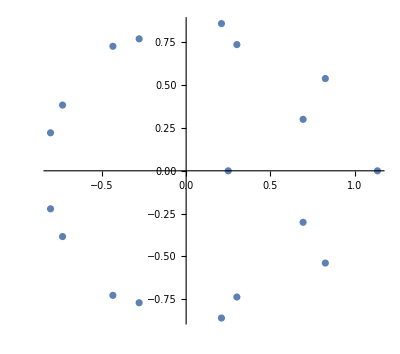

```mathematica
ComplexListPlot[v]
```

```mathematica
g[x_]=1-4 x-28 x^9-52 x^17+55 x^18
```

1-4 x-28 x^9-52 x^17+55 x^18

```mathematica
f[x_]=ExpandAll[x^18*g[1/x]]
```

55-52 x-28 x^9-4 x^17+x^18

```mathematica
1.216391661138265/1.136160638924951
```

1.07062

```mathematica
gout=dynamicNewtonPic[55-52 x-28 x^9-4 x^17+x^18,{x,-2-2*I,2+2*I},2000];
```

```mathematica
Export["dynamicNewtonPic_new_Salem_decioctic_18_toral_Inverse_A175739_PreAmp_exp4_2000res_lt9th.jpg",gout]
```

dynamicNewtonPic_new_Salem_decioctic_18_toral_Inverse_A175739_PreAmp_exp4_2000res_lt9th.jpg

```mathematica
(*end*)
```